```mathematica
Abs'[x_]:=Sign[x]
```

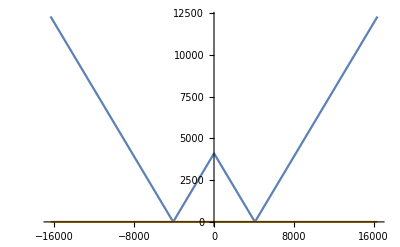

```mathematica
L:=8192 (*length of buffer*)
W:=4    (*some position for write pointer*)
CC[r_]:=Abs[Abs[W-r]-L/2] (* function to minimize *)
zz[s_]:=CC[s-CC'[s]*CC[s]] (* result of minimization applied to s (the input to CC[s]). To minimize, ofcourse we pushed s in the opposite direction of the derivative*)
(*CC[s] just happens to also give the magnitude of gradient needed to make CC[s + gradient] == 0*)
Plot[{CC[r],zz[3]}, {r,-2L,2L}]
```

```mathematica
CC2[r_, w_]:=Abs[Abs[w-r]-L/2]
zz2[x_,s_]:=CC2[x, s-(D[CC2[x,s], s])*CC2[x,s]]
Plot3D[{CC2[w,r],zz2[3]}, {r,-L,L},{w,-L,L}, AxesLabel->Automatic]
```

-Graphics3D-